Charles Rambo

# Homework 16.10

#### 5.36

[Computer] Consider a cart on a spring with natural frequency ωo= 2π, which is released from rest at xo= 1 and t = 0. Using appropriate graphing software, plot the position x (t) for 0 < t < 2 and for damping constants ,β = 0, 1, 2, 4, 6, 2π, 10, and 20. [Remember that x(t) is given by different formulas for β < ω0, β= ω0, and /3 > cool

```mathematica
ω0=2*π
v0=0
x0=1
t0=0
tf=2
βa=0
βb=1
βc=2
βd=4
βe=6
βf=2*π
βg=10
βh=20
 ωa=√(ω0^2-βa^2)
ωb=√(ω0^2-βb^2)
ωc=√(ω0^2-βc^2)
```

2 π

0

1

0

2

0

1

2

4

6

2 π

10

20

2 π

√(-1+4 π^2)

√(-4+4 π^2)

```mathematica
xa[t_] := x0*Exp[-βa*t]*Cos[ωa*t ]
xb[t_] := x0*Exp[-βb*t]*Cos[ωb*t ]
xc[t_] := x0*Exp[-βc*t]*Cos[ωc*t ]
xd[t_] := ((βd+√(βd^2-ω0^2))/(2βd))*Exp[-(βd-√(βd^2-ω0^2))*t]+((βd-√(βd^2-ω0^2))/(2βd))*Exp[-(βd+√(βd^2-ω0^2))*t](*tried NDSolve, but had to do this on paper*)
xe[t_] := ((βe+√(βe^2-ω0^2))/(2βe))*Exp[-(βe-√(βe^2-ω0^2))*t]+((βe-√(βe^2-ω0^2))/(2βe))*Exp[-(βe+√(βe^2-ω0^2))*t]
xf[t_] := Exp[-βf*t]+βf*t*Exp[-βf*t] (*again, after solving for constants, I feel like mathematica could solve that for us, but...*)
xg[t_] := ((βg+√(βg^2-ω0^2))/(2βg))*Exp[-(βg-√(βg^2-ω0^2))*t]+((βg-√(βg^2-ω0^2))/(2βg))*Exp[-(βg+√(βg^2-ω0^2))*t]
xh[t_] := ((βh+√(βh^2-ω0^2))/(2βh))*Exp[-(βh-√(βh^2-ω0^2))*t]+((βh-√(βh^2-ω0^2))/(2βh))*Exp[-(βh+√(βh^2-ω0^2))*t]
```

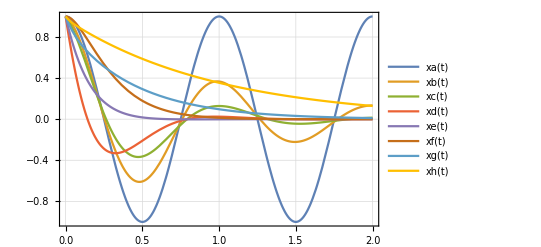

```mathematica
Plot[{xa[t],xb[t],xc[t],xd[t],xe[t],xf[t],xg[t],xh[t]},{t,t0,tf},PlotTheme->"Detailed",PlotRange->All,ImageSize->Full]
```